## Base model - analytic

```mathematica
Lambda[rh_,mh_,re_,me_]:=1/2 (re+rh-me-mh+√((-re-rh+me+mh)^2-4 (re rh-re me-rh mh)))
```

```mathematica
Lambdaratio[Rr_,m_]:=Lambda[Rr,m,1,m]
```

```mathematica
DLambdaDrho[rho_,m_]:=1/2 (1+(-1+rho)/(√((-1+rho)^2+4 m^2)))
```

```mathematica
DLambdaDt[rho_,m_]:=-1+(2 m)/(√((-1+rho)^2+4 m^2))
```

```mathematica
Solve[DLambdaDrho[rho,m]==-DLambdaDt[rho,m],m]
```

{{m→0},{m→-2/3 (-1+rho)}}

## Base model + global competition

```mathematica
eq1GC={D[nH[t],t]==rh*nH[t]-me*nH[t]+mh*nE[t]- k*nH[t]*(nE[t]+nH[t]),nH[0]==nH0}
```

{nH'[t]==mh nE[t]-me nH[t]+rh nH[t]-k nH[t] (nE[t]+nH[t]),nH[0]==nH0}

```mathematica
eq2GC={D[nE[t],t]==re*nE[t]-mh*nE[t]+me*nH[t] - k*nE[t]*(nE[t]+nH[t]),nE[0]==nE0}
```

{nE'[t]==-mh nE[t]+re nE[t]+me nH[t]-k nE[t] (nE[t]+nH[t]),nE[0]==nE0}

```mathematica
sysGC={eq1GC,eq2GC}
```

{{nH'[t]==mh nE[t]-me nH[t]+rh nH[t]-k nH[t] (nE[t]+nH[t]),nH[0]==nH0},{nE'[t]==-mh nE[t]+re nE[t]+me nH[t]-k nE[t] (nE[t]+nH[t]),nE[0]==nE0}}

```mathematica
Biglambda[tmax_,nh0_,ne0_,nhf_,nef_]:=(1/tmax)*Log[(nhf+nef)/(nh0+ne0)];
```

## Case1. nE0 = 1 and nH0 = 0, k=0, k= 0.1, k=1

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {0.01,0.2,0.5,1,5};
NE0B = 1;
NH0B = 0;
RE = 1;
Listk={0,10^-1,1};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.04}];
TabM = Flatten[{Table[i,{i,0,0.15,0.01}],Table[i,{i,0.175,2,0.025}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sysGC/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHORempl[[1,1,1]]
```

{re→1,rh→-0.99999,me→0.,mh→0.,k→0}

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,k->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sysGC/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sysGC/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO=Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM=Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRHO =  Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiM=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiM[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

### Plot

```mathematica
listcolor=Reverse[Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[tmaxB]-1)}]]
```

{RGBColor[1., 0.820127, 0.126955],RGBColor[1., 0.646929, 0.0801709],RGBColor[0.969963, 0.376081, 0.0322881],RGBColor[0.822129, 0.122225, 0.0039559],RGBColor[0.468742, 0., 0.0158236]}

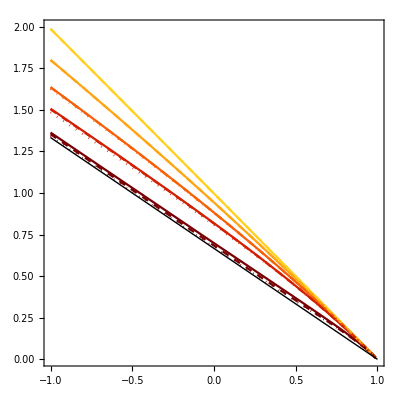

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->{{-1,1},{-0.00000001,2}},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,2]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Dashed,Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,2]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Dashed,Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,3]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Dotted,Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,3]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Dotted,Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{itmax,1,Length[tmaxB]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick],PlotRange->All]]
```

## Case2. nE0 = 0 and nH0 = 1, k=0, k= 0.01, k=0.1

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {5,7,10,20,50,100};
NE0B = 0;
NH0B = 1;
RE = 1;
Listk={0,10^-2,10^-1};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.03}];
TabM = Flatten[{Table[i,{i,0,0.2,0.01}],Table[i,{i,0.23,2,0.03}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sysGC/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001; (* percentage used to calculate derivatives*)
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,k->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sysGC/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sysGC/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO=Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM= Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRHO=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiM=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiM[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

### Plot

```mathematica
listcolor=Reverse[Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]]
```

{RGBColor[0.914809, 0.897673, 0.350652],RGBColor[0.5234324, 0.8244344, 0.4214008],RGBColor[0.2679184, 0.718234, 0.496156],RGBColor[0.1288222, 0.5597884, 0.5402974],RGBColor[0.0867346, 0.3233424, 0.5177146],RGBColor[0.122103, 0.00901808, 0.39826]}

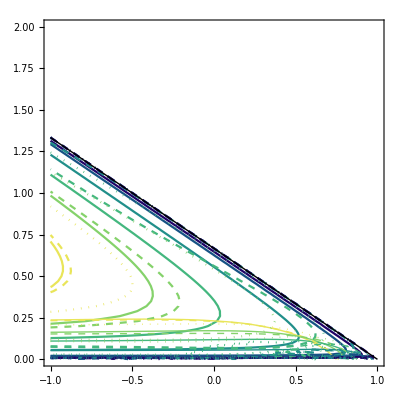

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->{{-1,1},{-0.0000001,2}},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thick,Opacity[1]],BaseStyle->{FontSize->16}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,2]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Dashed,Opacity[1]],BaseStyle->{FontSize->16}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,2]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thick,Dashed,Opacity[1]],BaseStyle->{FontSize->16}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,3]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Dotted,Opacity[1]],BaseStyle->{FontSize->16}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,3]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thick,Dotted,Opacity[1]],BaseStyle->{FontSize->16}],{itmax,1,Length[tmaxB]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick]]]
```